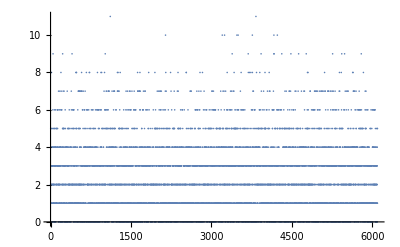

(0, 1, 2, 3, 4, 5, 6, 7, 8, 9,

```mathematica
rand=Abs[RandomVariate[NormalDistribution[0, 2], 6096]];
signal=Round[rand+Table[PDF[NormalDistribution[4000, 50],x]*10^4, {x, 1, 6096}]//N];
```

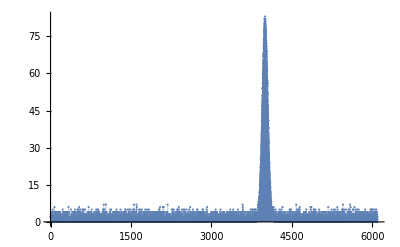

(2, 2, 2, 3, 0, 3, 4, 0, 0, 1, 3, 0, 0, 1, 0, 2, 1, 0, 3, 1, 0, 3, 1, 4, 0, 1, 1, 1, 2, 2, 2, 1, 0, 2, 1, 1, 1, 1, 3, 2, 4, 5, 2, 1, 1, 2, 1, 2, 0, 3, 2, 1, 2, 2, 1, 1, 1, 0, 1, 1, 1, 0, 3, 2, 4, 2, 2, 1, 2, 2, 1, 0, 1, 6, 1, 0, 2, 1, 1, 4, 1, 1, 1, 3, 1, 2, 2, 2, 4, 1, 0, 3, 1, 4, 0, 2, 0, 2, 3, 0, 3, 1, 3, 3, 1, 1, 4, 1, 4, 3, 1, 3, 2, 2, 2, 2, 0, 1, 1, 2, 1, 3, 0, 2, 3, 1, 0, 1, 0, 1, 4, 0, 2, 2, 0, 1, 2, 1, 0, 2, 2, 0, 3, 0, 4, 0, 2, 1, 1, 2, 0, 2, 1, 0, 1, 4, 1, 1, 1, 4, 2, 1, 4, 1, 0, 1, 3, 2, 2, 3, 0, 1, 2, 3, 1, 1, 1, 2, 0, 1, 0, 2, 2, 4, 1, 2, 1, 2, 2, 1, 1, 2, 3, 3, 1, 0, 2, 1, 0, 0, 3, 0, 2, 2, 2, 0, 1, 1, 2, 1, 1, 0, 0, 0, 0, 2, 1, 2, 2, 2, 2, 0, 2, 2, 1, 5, 1, 1, 2, 2, 2, 1, 3, 3, 1, 2, 4, 3, 1, 0, 2, 0, 1, 4, 3, 1, 2, 1, 1, 1, 2, 3, 1, 2, 3, 0, 1, 2, 1, 1, 2, 0, 0, 0, 4, 2, 1, 4, 1, 2, 2, 1, 3, 1, 1, 2, 2, 1, 1, 4, 1, 3, 1, 4, 3, 1, 4, 2, 4, 2, 2, 3, 1, 2, 1, 4, 1, 0, 1, 4, 3, 2, 2, 2, 4, 2, 2, 1, 0, 0, 1, 3, 0, 2, 3, 2, 1, 1, 1, 1, 0, 1, 0, 0, 0, 2, 2, 3, 2, 1, 1, 1, 0, 6, 0, 4, 2, 4, 3, 1, 0, 0, 0, 2, 2, 0, 1, 1, 4, 1, 2, 1, 1, 1, 1, 0, 0, 2, 0, 1, 1, 1, 1, 1, 1, 2, 1, 1, 2, 1, 2, 1, 2, 1, 0, 1, 0, 0, 2, 2, 5, 0, 2, 1, 1, 1, 1, 3, 2, 3, 1, 2, 2, 1, 2, 1, 1, 1, 2, 2, 1, 0, 1, 0, 2, 0, 2, 2, 0, 4, 4, 0, 0, 1, 3, 2, 1, 1, 0, 2, 1, 1, 3, 2, 3, 1, 0, 0, 2, 0, 2, 4, 3, 1, 4, 1, 2, 2, 1, 2, 1, 0, 1, 3, 2, 0, 2, 0, 1, 1, 1, 4, 1, 4, 0, 0, 5, 3, 3, 2, 3, 1, 0, 1, 4, 1, 2, 1, 3, 1, 1, 2, 1, 3, 1, 2, 4, 0, 2, 4, 2, 1, 1, 2, 0, 1, 1, 1, 1, 1, 1, 2, 3, 0, 2, 0, 1, 3, 2, 2, 1, 1, 1, 0, 5, 3, 1, 5, 3, 3, 1, 1, 0, 2, 1, 4, 0, 2, 0, 1, 1, 2, 2, 4, 5, 1, 3, 4, 0, 1, 0, 6, 2, 1, 1, 2, 2, 1, 2, 4, 0, 4, 3, 3, 1, 3, 2, 1, 2, 3, 2, 1, 2, 5, 3, 0, 0, 1, 2, 4, 1, 1, 2, 0, 0, 2, 1, 0, 0, 3, 0, 1, 2, 1, 2, 1, 1, 1, 3, 0, 3, 2, 1, 1, 1, 1, 0, 2, 3, 3, 4, 0, 1, 1, 3, 1, 5, 3, 1, 1, 2, 2, 4, 0, 5, 0, 2, 1, 1, 1, 1, 0, 2, 3, 1, 2, 3, 2, 1, 2, 0, 5, 3, 2, 0, 2, 1, 1, 3, 3, 3, 0, 0, 0, 3, 3, 2, 1, 1, 0, 2, 1, 0, 0, 5, 0, 1, 1, 1, 3, 2, 1, 1, 0, 2, 2, 2, 2, 0, 1, 1, 1, 2, 1, 3, 1, 1, 1, 3, 1, 0, 0, 2, 1, 2, 2, 2, 1, 3, 0, 2, 1, 0, 1, 1, 1, 3, 0, 1, 4, 2, 1, 0, 1, 1, 3, 3, 0, 1, 1, 0, 1, 1, 2, 1, 0, 1, 4, 4, 6, 0, 1, 3, 2, 0, 2, 4, 1, 0, 1, 4, 0, 1, 1, 3, 3, 3, 2, 2, 1, 2, 2, 1, 1, 1, 1, 4, 2, 3, 1, 2, 0, 2, 2, 2, 1, 2, 2, 1, 1, 0, 3, 3, 2, 1, 1, 1, 2, 3, 0, 2, 2, 2, 2, 4, 1, 5, 1, 3, 2, 0, 1, 1, 3, 0, 1, 1, 0, 0, 1, 0, 2, 2, 3, 0, 2, 2, 2, 1, 3, 3, 3, 1, 0, 2, 1, 0, 0, 0, 0, 1, 0, 0, 1, 3, 1, 1, 2, 1, 1, 1, 1, 3, 1, 1, 4, 2, 0, 1, 1, 4, 1, 2, 3, 2, 3, 1, 1, 1, 2, 3, 0, 2, 2, 2, 3, 0, 2, 2, 2, 2, 1, 1, 0, 1, 0, 1, 4, 1, 2, 5, 2, 0, 0, 1, 2, 1, 1, 1, 3, 3, 2, 4, 0, 3, 1, 2, 1, 1, 1, 3, 3, 1, 4, 1, 0, 1, 4, 3, 1, 5, 2, 1, 1, 0, 3, 2, 0, 1, 5, 2, 1, 4, 3, 1, 2, 2, 0, 1, 0, 1, 2, 1, 3, 3, 2, 2, 2, 0, 4, 1, 3, 1, 0, 2, 0, 3, 2, 1, 2, 1, 2, 2, 1, 0, 2, 3, 3, 1, 1, 1, 1, 0, 3, 1, 2, 2, 1, 2, 3, 1, 3, 2, 1, 1, 1, 3, 3, 0, 3, 2, 1, 2, 1, 1, 1, 0, 1, 2, 3, 0, 2, 0, 2, 3, 2, 2, 1, 1, 2, 4, 0, 1, 2, 2, 2, 2, 2, 0, 5, 4, 0, 0, 1, 5, 3, 0, 4, 4, 1, 2, 7, 3, 2, 2, 2, 1, 1, 1, 3, 1, 1, 1, 1, 0, 2, 1, 1, 5, 0, 2, 1, 4, 0, 2, 2, 0, 1, 0, 2, 2, 2, 3, 2, 1, 3, 2, 3, 0, 4, 1, 7, 0, 2, 1, 2, 2, 1, 1, 2, 4, 0, 2, 2, 4, 1, 3, 1, 0, 0, 1, 0, 1, 0, 2, 1, 1, 1, 0, 2, 1, 1, 1, 1, 0, 1, 3, 1, 1, 0, 1, 1, 1, 2, 3, 2, 2, 1, 1, 1, 0, 1, 3, 2, 3, 1, 1, 2, 1, 0, 1, 1, 1, 2, 1, 2, 2, 1, 2, 1, 2, 0, 2, 3, 4, 1, 0, 0, 1, 4, 1, 1, 5, 3, 2, 2, 2, 3, 2, 1, 3, 2, 1, 0, 0, 0, 2, 5, 1, 0, 1, 1, 1, 0, 1, 3, 2, 1, 1, 0, 1, 2, 0, 2, 1, 1, 0, 0, 3, 1, 0, 3, 0, 2, 0, 1, 2, 2, 2, 3, 3, 2, 1, 2, 2, 1, 1, 4, 2, 1, 1, 2, 3, 2, 4, 2, 3, 2, 4, 0, 2, 2, 2, 3, 1, 4, 2, 2, 0, 1, 2, 0, 1, 1, 2, 1, 2, 0, 1, 3, 1, 1, 2, 1, 0, 1, 2, 1, 2, 1, 1, 4, 1, 4, 0, 0, 2, 0, 1, 1, 0, 2, 3, 0, 0, 2, 3, 3, 5, 1, 1, 3, 4, 3, 2, 1, 0, 0, 0, 4, 2, 4, 2, 3, 0, 2, 1, 3, 2, 1, 2, 1, 4, 0, 2, 2, 2, 1, 0, 0, 4, 3, 1, 3, 1, 3, 0, 2, 3, 2, 2, 2, 0, 2, 2, 2, 0, 3, 1, 2, 4, 1, 0, 2, 0, 2, 1, 0, 2, 1, 1, 0, 1, 0, 2, 0, 0, 1, 0, 3, 0, 1, 3, 2, 3, 5, 3, 0, 3, 0, 1, 2, 0, 1, 1, 3, 2, 1, 4, 0, 2, 2, 3, 2, 1, 1, 3, 0, 0, 1, 2, 1, 1, 2, 2, 2, 1, 0, 1, 0, 2, 1, 1, 3, 0, 1, 0, 1, 1, 0, 3, 0, 2, 2, 1, 1, 4, 1, 1, 3, 1, 4, 4, 0, 3, 1, 0, 0, 0, 1, 3, 1, 4, 2, 3, 2, 3, 1, 2, 1, 3, 1, 2, 2, 2, 1, 2, 0, 0, 2, 2, 1, 4, 0, 5, 4, 1, 1, 5, 0, 2, 0, 1, 3, 1, 1, 4, 2, 0, 0, 0, 2, 1, 1, 1, 0, 2, 3, 0, 1, 3, 1, 1, 2, 1, 1, 2, 1, 3, 1, 0, 1, 0, 1, 1, 2, 1, 1, 3, 1, 5, 1, 0, 0, 1, 1, 2, 1, 3, 0, 0, 1, 2, 0, 0, 0, 1, 3, 4, 0, 2, 5, 1, 1, 1, 4, 3, 1, 1, 1, 2, 1, 3, 1, 0, 1, 1, 1, 1, 2, 2, 2, 0, 1, 2, 0, 2, 3, 0, 1, 1, 3, 0, 3, 2, 5, 3, 3, 0, 1, 0, 2, 2, 1, 4, 1, 1, 1, 2, 1, 2, 2, 0, 2, 2, 2, 0, 1, 2, 0, 1, 1, 1, 3, 0, 2, 3, 4, 2, 2, 2, 2, 2, 0, 2, 2, 4, 2, 2, 1, 0, 1, 3, 1, 0, 5, 1, 2, 5, 0, 5, 1, 0, 7, 1, 1, 3, 0, 4, 2, 1, 1, 0, 4, 0, 1, 1, 0, 1, 0, 1, 2, 0, 1, 1, 2, 1, 3, 0, 1, 2, 2, 1, 2, 0, 2, 3, 1, 0, 1, 4, 1, 4, 1, 1, 2, 2, 2, 2, 0, 5, 2, 7, 1, 1, 1, 2, 1, 1, 6, 0, 3, 2, 1, 2, 1, 0, 0, 2, 1, 1, 3, 0, 1, 1, 0, 1, 1, 2, 2, 3, 1, 1, 2, 0, 1, 1, 3, 0, 1, 1, 1, 3, 3, 1, 1, 1, 1, 1, 1, 4, 5, 1, 1, 1, 3, 1, 1, 2, 2, 1, 3, 1, 2, 0, 1, 0, 4, 5, 0, 1, 1, 4, 1, 2, 2, 0, 2, 3, 0, 0, 1, 4, 2, 4, 2, 0, 1, 0, 2, 0, 1, 1, 0, 0, 1, 1, 0, 2, 0, 4, 0, 1, 5, 0, 2, 1, 3, 1, 1, 3, 2, 1, 0, 0, 2, 2, 1, 2, 2, 1, 2, 1, 0, 1, 0, 2, 0, 0, 3, 3, 0, 1, 4, 1, 0, 1, 0, 1, 1, 1, 1, 1, 1, 1, 3, 4, 1, 2, 1, 2, 1, 1, 4, 1, 1, 2, 2, 0, 3, 1, 3, 0, 2, 1, 5, 1, 2, 3, 1, 4, 1, 1, 2, 1, 3, 0, 1, 1, 2, 3, 2, 2, 0, 0, 1, 2, 2, 0, 2, 0, 4, 1, 1, 1, 0, 0, 0, 3, 5, 3, 1, 3, 2, 2, 2, 1, 2, 1, 3, 2, 2, 4, 0, 1, 2, 4, 1, 2, 1, 2, 1, 2, 0, 0, 0, 0, 1, 1, 1, 0, 1, 5, 2, 0, 1, 4, 2, 1, 1, 0, 1, 3, 1, 1, 0, 2, 1, 3, 0, 0, 1, 3, 2, 3, 1, 1, 1, 2, 4, 3, 0, 3, 2, 1, 2, 1, 2, 2, 1, 3, 1, 4, 1, 1, 2, 1, 1, 1, 1, 3, 1, 0, 2, 1, 1, 1, 1, 2, 0, 2, 3, 0, 2, 1, 3, 1, 3, 2, 0, 4, 1, 1, 2, 2, 1, 1, 3, 2, 2, 4, 2, 0, 1, 1, 0, 0, 1, 1, 2, 4, 3, 1, 1, 1, 1, 2, 1, 0, 2, 0, 1, 4, 1, 1, 4, 1, 1, 1, 3, 1, 2, 1, 1, 1, 3, 3, 3, 0, 0, 3, 1, 2, 1, 0, 0, 3, 2, 1, 0, 1, 4, 3, 2, 0, 2, 0, 0, 4, 3, 1, 1, 3, 2, 0, 2, 2, 1, 3, 1, 2, 2, 3, 3, 1, 1, 2, 1, 1, 4, 2, 3, 0, 0, 3, 2, 3, 2, 0, 2, 3, 4, 1, 4, 2, 0, 1, 2, 0, 1, 1, 3, 0, 3, 0, 2, 3, 1, 4, 5, 3, 3, 2, 3, 1, 1, 1, 4, 1, 5, 3, 2, 2, 0, 1, 2, 1, 3, 1, 2, 6, 2, 3, 4, 0, 1, 3, 0, 0, 4, 1, 0, 1, 0, 0, 2, 4, 1, 3, 3, 1, 2, 2, 3, 3, 0, 2, 0, 1, 4, 1, 1, 4, 1, 1, 1, 1, 2, 0, 4, 1, 1, 2, 1, 1, 2, 3, 0, 3, 3, 3, 6, 3, 1, 2, 1, 1, 2, 0, 1, 3, 2, 0, 0, 1, 1, 1, 2, 0, 1, 4, 6, 2, 0, 2, 4, 1, 3, 2, 1, 2, 2, 2, 2, 2, 1, 0, 0, 2, 4, 2, 0, 0, 1, 1, 1, 1, 1, 0, 2, 0, 1, 1, 0, 2, 0, 1, 0, 0, 2, 2, 1, 3, 2, 2, 3, 1, 2, 1, 4, 3, 1, 1, 0, 1, 0, 3, 2, 1, 2, 1, 1, 1, 4, 2, 3, 0, 2, 2, 4, 1, 1, 7, 2, 0, 2, 1, 3, 0, 0, 2, 1, 0, 1, 1, 1, 2, 0, 0, 2, 0, 1, 2, 3, 1, 3, 1, 3, 1, 1, 0, 0, 3, 0, 1, 0, 2, 2, 1, 3, 0, 2, 0, 1, 0, 0, 1, 1, 1, 2, 1, 3, 1, 0, 1, 0, 3, 1, 2, 2, 0, 1, 1, 0, 1, 2, 0, 2, 1, 0, 1, 0, 1, 1, 1, 0, 2, 1, 2, 5, 0, 1, 3, 1, 3, 2, 1, 1, 2, 1, 1, 0, 4, 1, 2, 5, 1, 0, 1, 2, 0, 4, 2, 3, 3, 4, 4, 1, 0, 2, 1, 1, 1, 1, 1, 0, 1, 0, 5, 0, 2, 1, 3, 1, 0, 3, 2, 1, 0, 3, 1, 3, 1, 1, 2, 1, 2, 1, 2, 0, 2, 1, 1, 1, 0, 2, 1, 0, 4, 2, 1, 4, 2, 2, 1, 2, 3, 3, 2, 1, 4, 0, 2, 1, 3, 1, 2, 1, 3, 2, 1, 3, 1, 0, 2, 1, 1, 3, 4, 2, 4, 1, 1, 1, 5, 2, 5, 2, 1, 1, 3, 2, 4, 3, 2, 1, 0, 1, 0, 1, 0, 3, 1, 2, 2, 2, 1, 2, 2, 6, 0, 2, 0, 5, 3, 1, 1, 1, 3, 4, 1, 3, 2, 4, 3, 1, 1, 1, 3, 3, 0, 1, 0, 1, 1, 3, 3, 1, 2, 0, 1, 1, 2, 2, 0, 1, 3, 2, 1, 4, 0, 0, 1, 0, 3, 2, 1, 1, 1, 2, 3, 2, 1, 2, 3, 2, 0, 1, 5, 3, 0, 2, 2, 3, 1, 1, 2, 2, 3, 2, 2, 2, 1, 3, 2, 0, 2, 1, 2, 1, 1, 1, 2, 2, 5, 4, 2, 2, 0, 1, 0, 2, 1, 1, 0, 1, 1, 1, 2, 1, 1, 1, 0, 3, 2, 0, 0, 2, 1, 2, 5, 1, 4, 1, 2, 2, 2, 1, 1, 4, 2, 2, 4, 3, 1, 2, 1, 2, 1, 0, 3, 2, 3, 1, 1, 0, 0, 1, 2, 2, 1, 1, 0, 1, 1, 3, 0, 5, 3, 2, 0, 0, 1, 1, 1, 1, 0, 3, 3, 0, 1, 2, 1, 1, 1, 3, 0, 1, 2, 0, 2, 1, 4, 1, 3, 3, 1, 3, 2, 2, 1, 1, 3, 1, 0, 1, 3, 1, 2, 3, 1, 2, 2, 1, 2, 5, 1, 2, 2, 2, 2, 0, 1, 1, 1, 1, 2, 3, 2, 1, 4, 1, 6, 2, 2, 1, 1, 0, 2, 1, 0, 1, 2, 3, 3, 1, 2, 2, 1, 3, 0, 2, 1, 0, 0, 2, 1, 0, 0, 2, 4, 3, 1, 0, 0, 0, 2, 0, 2, 4, 1, 3, 1, 3, 2, 2, 1, 0, 1, 2, 3, 0, 1, 3, 5, 1, 1, 0, 1, 1, 1, 1, 1, 1, 0, 3, 2, 1, 3, 0, 3, 0, 0, 1, 2, 4, 2, 3, 4, 1, 0, 0, 0, 0, 2, 0, 1, 2, 1, 2, 3, 1, 0, 4, 0, 1, 1, 1, 1, 1, 0, 1, 1, 0, 3, 2, 1, 1, 0, 3, 2, 2, 1, 2, 2, 3, 1, 1, 1, 1, 0, 0, 1, 2, 1, 1, 1, 3, 0, 1, 1, 4, 3, 1, 0, 4, 4, 5, 5, 1, 2, 1, 1, 0, 3, 1, 0, 2, 3, 1, 0, 0, 1, 1, 0, 4, 0, 1, 0, 0, 0, 0, 2, 3, 4, 3, 1, 0, 2, 3, 0, 4, 0, 0, 0, 3, 1, 2, 3, 1, 2, 3, 4, 3, 0, 2, 1, 1, 2, 1, 1, 1, 1, 4, 2, 3, 3, 1, 3, 0, 1, 4, 2, 0, 1, 2, 2, 0, 1, 0, 3, 1, 2, 3, 2, 2, 4, 2, 1, 1, 0, 3, 2, 1, 3, 0, 0, 0, 0, 4, 4, 1, 1, 4, 3, 0, 5, 0, 5, 1, 3, 2, 0, 0, 0, 3, 3, 1, 3, 2, 1, 1, 1, 2, 1, 2, 2, 0, 3, 4, 1, 1, 2, 3, 2, 1, 1, 2, 1, 3, 4, 0, 1, 2, 1, 1, 2, 1, 2, 3, 2, 1, 1, 0, 3, 2, 1, 1, 1, 2, 3, 2, 2, 1, 0, 1, 1, 1, 1, 2, 0, 0, 1, 4, 1, 2, 2, 1, 2, 5, 1, 1, 2, 1, 0, 2, 2, 6, 1, 0, 0, 4, 2, 3, 3, 1, 1, 1, 0, 2, 0, 3, 3, 2, 1, 3, 3, 0, 0, 1, 0, 2, 1, 1, 2, 0, 1, 0, 2, 1, 1, 0, 2, 1, 1, 2, 1, 1, 0, 0, 1, 2, 1, 1, 3, 1, 0, 0, 0, 0, 2, 0, 3, 0, 2, 1, 2, 0, 2, 1, 3, 0, 2, 2, 0, 1, 0, 0, 2, 1, 0, 1, 4, 3, 1, 3, 2, 2, 1, 2, 2, 3, 1, 2, 0, 1, 3, 4, 3, 2, 4, 1, 2, 1, 0, 1, 1, 0, 3, 0, 2, 0, 2, 3, 0, 4, 1, 2, 2, 2, 2, 3, 1, 1, 1, 0, 2, 1, 2, 0, 0, 2, 1, 2, 1, 0, 4, 3, 1, 3, 4, 3, 0, 1, 0, 1, 4, 1, 0, 2, 3, 4, 1, 2, 3, 1, 0, 1, 1, 3, 3, 1, 1, 2, 4, 0, 3, 5, 1, 4, 0, 0, 2, 3, 2, 4, 0, 0, 0, 2, 3, 2, 4, 4, 3, 3, 0, 1, 2, 1, 4, 4, 2, 2, 0, 2, 1, 2, 2, 0, 1, 1, 3, 1, 1, 1, 1, 1, 0, 0, 2, 1, 1, 2, 3, 1, 1, 1, 3, 0, 2, 2, 0, 1, 0, 1, 3, 1, 1, 1, 1, 0, 1, 1, 3, 2, 0, 2, 1, 1, 1, 1, 1, 2, 1, 1, 2, 1, 2, 4, 0, 1, 0, 3, 3, 2, 1, 2, 5, 1, 0, 0, 1, 0, 1, 1, 1, 0, 1, 2, 3, 1, 3, 3, 0, 0, 1, 1, 0, 1, 3, 0, 3, 2, 0, 1, 2, 4, 2, 0, 1, 0, 2, 1, 1, 2, 1, 1, 0, 2, 1, 1, 3, 1, 2, 1, 1, 0, 3, 0, 0, 2, 1, 0, 4, 0, 2, 1, 0, 3, 2, 2, 1, 1, 2, 4, 0, 4, 1, 1, 0, 0, 0, 1, 1, 3, 1, 1, 1, 2, 3, 2, 1, 1, 0, 1, 1, 1, 1, 0, 3, 0, 0, 3, 2, 0, 1, 0, 2, 2, 0, 3, 1, 0, 1, 0, 1, 0, 3, 3, 2, 0, 2, 0, 3, 1, 1, 4, 3, 3, 1, 1, 4, 2, 2, 0, 0, 0, 2, 1, 0, 1, 0, 2, 3, 4, 1, 0, 2, 0, 2, 1, 0, 0, 1, 3, 2, 2, 2, 3, 0, 1, 1, 3, 3, 2, 1, 2, 1, 2, 3, 0, 4, 3, 1, 2, 2, 1, 1, 0, 1, 2, 0, 2, 1, 1, 0, 3, 1, 5, 1, 2, 2, 1, 1, 1, 4, 2, 3, 4, 2, 1, 1, 1, 1, 0, 0, 3, 3, 2, 2, 0, 1, 1, 3, 1, 3, 1, 4, 1, 1, 1, 2, 0, 1, 2, 0, 0, 2, 1, 3, 0, 1, 3, 0, 0, 2, 3, 1, 3, 2, 2, 1, 2, 5, 4, 4, 1, 0, 0, 1, 4, 1, 1, 2, 1, 1, 1, 2, 3, 1, 3, 1, 3, 4, 2, 0, 2, 1, 0, 0, 3, 3, 2, 1, 3, 2, 4, 2, 3, 2, 0, 1, 2, 3, 3, 0, 0, 3, 0, 2, 1, 3, 3, 1, 1, 2, 1, 1, 0, 2, 3, 1, 4, 2, 1, 1, 0, 0, 1, 2, 2, 3, 1, 3, 2, 1, 2, 2, 0, 0, 0, 2, 4, 2, 4, 2, 2, 1, 1, 3, 2, 1, 2, 4, 5, 3, 1, 2, 1, 1, 1, 2, 1, 1, 1, 3, 1, 1, 0, 2, 0, 2, 0, 1, 2, 1, 2, 2, 1, 0, 0, 1, 0, 4, 1, 0, 1, 1, 0, 2, 0, 3, 0, 3, 2, 0, 1, 1, 1, 0, 0, 1, 1, 3, 3, 1, 0, 2, 1, 2, 2, 3, 4, 2, 1, 2, 2, 4, 2, 1, 2, 1, 0, 1, 2, 2, 0, 3, 0, 1, 3, 2, 2, 0, 1, 2, 0, 0, 2, 4, 7, 6, 0, 2, 1, 0, 1, 0, 5, 1, 1, 0, 1, 1, 1, 1, 1, 1, 1, 2, 1, 0, 3, 2, 0, 1, 0, 1, 4, 3, 0, 2, 1, 1, 1, 1, 4, 2, 3, 2, 1, 2, 1, 0, 1, 0, 2, 0, 1, 1, 1, 1, 2, 0, 2, 4, 1, 2, 2, 0, 0, 2, 0, 0, 1, 0, 3, 2, 2, 1, 2, 1, 0, 2, 2, 1, 3, 1, 0, 1, 0, 0, 1, 1, 2, 4, 2, 1, 3, 3, 2, 2, 0, 1, 2, 1, 4, 1, 0, 2, 3, 4, 3, 2, 4, 2, 3, 2, 1, 1, 2, 1, 1, 1, 2, 0, 2, 1, 1, 3, 0, 0, 2, 0, 4, 1, 0, 2, 2, 1, 0, 2, 2, 2, 4, 3, 2, 3, 2, 0, 0, 0, 1, 2, 3, 3, 4, 0, 1, 5, 0, 0, 1, 2, 2, 0, 1, 0, 0, 1, 1, 2, 1, 2, 1, 1, 2, 0, 0, 0, 3, 2, 2, 1, 1, 5, 2, 1, 4, 1, 1, 1, 5, 2, 1, 1, 1, 0, 0, 3, 3, 1, 3, 4, 4, 1, 4, 0, 1, 4, 2, 3, 4, 4, 3, 1, 1, 0, 1, 0, 3, 1, 3, 2, 5, 2, 1, 0, 2, 0, 5, 2, 2, 0, 1, 1, 1, 2, 3, 3, 4, 2, 3, 2, 5, 1, 1, 1, 3, 3, 3, 1, 0, 1, 1, 2, 1, 0, 5, 2, 3, 0, 3, 0, 1, 4, 2, 1, 2, 2, 1, 3, 1, 1, 2, 4, 4, 1, 1, 3, 2, 2, 2, 4, 2, 3, 2, 3, 3, 2, 3, 4, 2, 3, 7, 3, 3, 3, 4, 4, 4, 6, 8, 6, 6, 5, 5, 5, 7, 6, 6, 6, 9, 6, 6, 10, 7, 7, 8, 10, 9, 12, 10, 9, 10, 10, 10, 11, 12, 13, 15, 13, 15, 16, 15, 15, 17, 17, 18, 20, 22, 18, 19, 19, 20, 22, 21, 23, 25, 23, 26, 25, 26, 26, 27, 29, 31, 30, 30, 33, 32, 35, 34, 36, 36, 37, 38, 38, 41, 42, 42, 45, 44, 47, 47, 47, 48, 49, 50, 51, 51, 54, 54, 54, 58, 56, 60, 58, 60, 59, 61, 64, 62, 64, 64, 65, 67, 68, 67, 68, 68, 70, 71, 72, 71, 74, 73, 74, 74, 77, 76, 78, 78, 80, 77, 79, 78, 79, 82, 82, 80, 81, 81, 80, 80, 81, 81, 83, 82, 80, 81, 81, 81, 80, 82, 80, 81, 79, 78, 79, 79, 78, 77, 76, 77, 76, 78, 76, 75, 73, 73, 72, 72, 71, 70, 69, 69, 71, 67, 68, 69, 65, 63, 63, 62, 64, 62, 61, 61, 58, 57, 56, 56, 55, 57, 56, 52, 52, 52, 49, 47, 47, 45, 44, 46, 43, 41, 44, 41, 41, 38, 38, 38, 35, 36, 33, 34, 32, 33, 32, 29, 28, 27, 27, 26, 26, 24, 23, 24, 23, 22, 21, 20, 19, 19, 18, 20, 17, 17, 17, 16, 15, 16, 13, 14, 12, 13, 16, 11, 14, 12, 10, 9, 11, 10, 12, 8, 8, 8, 8, 8, 7, 7, 9, 7, 8, 5, 5, 5, 6, 4, 4, 5, 6, 6, 5, 4, 3, 5, 3, 3, 3, 4, 4, 5, 2, 2, 5, 4, 2, 2, 2, 3, 3, 2, 1, 2, 3, 2, 6, 3, 3, 5, 1, 2, 1, 1, 6, 3, 1, 1, 3, 1, 3, 5, 2, 1, 1, 1, 1, 2, 3, 4, 4, 1, 3, 2, 3, 0, 2, 1, 2, 1, 3, 2, 0, 1, 0, 2, 2, 1, 4, 1, 1, 4, 0, 2, 5, 1, 0, 1, 2, 2, 1, 4, 2, 1, 2, 2, 0, 1, 1, 0, 1, 2, 2, 3, 2, 3, 1, 0, 1, 1, 2, 2, 2, 2, 1, 0, 1, 0, 2, 0, 0, 2, 3, 2, 1, 0, 1, 1, 1, 2, 1, 0, 0, 4, 3, 1, 1, 1, 4, 2, 4, 3, 3, 4, 2, 3, 1, 2, 2, 3, 2, 1, 2, 4, 1, 5, 2, 2, 0, 0, 2, 1, 3, 3, 0, 1, 2, 1, 1, 1, 4, 1, 2, 2, 0, 4, 1, 1, 1, 2, 3, 3, 0, 4, 1, 2, 5, 0, 0, 1, 1, 4, 2, 2, 3, 1, 1, 4, 2, 1, 2, 0, 1, 0, 1, 0, 3, 2, 0, 0, 1, 6, 1, 0, 2, 1, 3, 1, 0, 0, 1, 1, 2, 0, 0, 0, 2, 1, 1, 2, 3, 3, 3, 1, 1, 1, 0, 0, 1, 4, 1, 3, 1, 1, 0, 0, 0, 3, 1, 1, 4, 2, 3, 1, 4, 1, 2, 3, 2, 2, 2, 1, 1, 2, 1, 2, 1, 2, 1, 2, 0, 1, 1, 1, 1, 2, 1, 1, 1, 0, 1, 0, 0, 3, 2, 0, 2, 1, 1, 2, 0, 0, 0, 2, 3, 4, 1, 2, 2, 3, 1, 1, 1, 1, 3, 1, 0, 1, 2, 2, 2, 2, 1, 1, 1, 2, 2, 0, 0, 1, 2, 0, 2, 0, 0, 2, 0, 3, 2, 2, 4, 1, 1, 0, 1, 3, 2, 2, 0, 4, 2, 5, 2, 1, 3, 0, 3, 0, 1, 3, 4, 2, 2, 0, 1, 1, 0, 2, 3, 1, 5, 2, 1, 1, 1, 2, 0, 1, 1, 1, 1, 5, 1, 2, 1, 1, 2, 2, 1, 2, 1, 1, 2, 2, 1, 1, 2, 3, 2, 0, 4, 1, 4, 1, 2, 3, 1, 1, 1, 1, 1, 1, 3, 0, 3, 2, 1, 0, 2, 0, 1, 1, 3, 1, 3, 2, 1, 0, 1, 4, 2, 3, 1, 0, 0, 1, 2, 0, 0, 1, 2, 1, 3, 1, 1, 1, 1, 3, 2, 1, 1, 1, 1, 2, 0, 2, 0, 1, 1, 3, 3, 4, 1, 1, 1, 2, 1, 4, 0, 4, 1, 3, 3, 1, 0, 4, 7, 0, 3, 3, 2, 4, 1, 3, 1, 3, 1, 5, 1, 1, 0, 0, 0, 3, 2, 3, 0, 3, 0, 1, 2, 2, 2, 2, 2, 1, 4, 0, 4, 1, 3, 5, 2, 2, 2, 1, 0, 1, 1, 0, 0, 1, 2, 0, 2, 4, 1, 0, 3, 5, 1, 3, 3, 1, 5, 1, 0, 1, 5, 4, 0, 0, 6, 0, 2, 2, 2, 3, 2, 3, 1, 1, 1, 1, 0, 1, 2, 3, 3, 1, 1, 1, 2, 0, 1, 1, 1, 1, 1, 1, 1, 2, 1, 1, 2, 1, 0, 0, 3, 2, 1, 2, 0, 1, 0, 1, 1, 0, 1, 0, 1, 1, 1, 3, 2, 1, 1, 0, 3, 1, 1, 3, 1, 0, 1, 0, 2, 3, 1, 1, 0, 0, 3, 0, 1, 1, 0, 3, 1, 2, 2, 2, 4, 2, 4, 0, 1, 2, 2, 0, 2, 0, 2, 3, 3, 0, 1, 3, 0, 1, 1, 1, 0, 1, 1, 2, 2, 1, 4, 2, 0, 1, 2, 3, 0, 3, 4, 2, 3, 0, 0, 1, 2, 1, 2, 5, 1, 1, 3, 0, 2, 1, 0, 1, 1, 1, 3, 1, 1, 0, 0, 0, 2, 2, 3, 1, 1, 1, 3, 1, 0, 3, 0, 2, 2, 3, 1, 2, 1, 1, 1, 1, 1, 2, 2, 1, 0, 3, 2, 2, 1, 0, 2, 1, 2, 3, 4, 1, 2, 2, 2, 0, 2, 4, 1, 3, 1, 2, 2, 1, 0, 1, 1, 1, 0, 1, 1, 0, 2, 0, 0, 6, 3, 3, 0, 5, 2, 0, 1, 3, 0, 1, 3, 1, 1, 0, 2, 2, 0, 6, 0, 1, 1, 1, 1, 3, 2, 0, 2, 4, 1, 4, 1, 2, 1, 1, 4, 1, 2, 3, 0, 3, 2, 0, 3, 1, 3, 2, 2, 1, 4, 1, 1, 0, 4, 3, 2, 3, 2, 0, 3, 5, 1, 1, 1, 2, 2, 2, 0, 2, 1, 1, 2, 3, 2, 1, 1, 0, 3, 0, 3, 5, 2, 2, 0, 2, 4, 2, 1, 3, 1, 0, 3, 1, 5, 3, 4, 1, 4, 0, 0, 1, 2, 0, 1, 1, 2, 1, 2, 0, 2, 1, 1, 2, 1, 2, 2, 4, 1, 0, 2, 0, 0, 1, 2, 3, 2, 2, 1, 2, 1, 1, 1, 3, 1, 1, 3, 1, 2, 1, 3, 1, 2, 0, 2, 2, 1, 0, 0, 2, 0, 3, 1, 0, 1, 1, 0, 1, 3, 3, 3, 0, 3, 3, 2, 5, 4, 3, 1, 4, 3, 0, 1, 2, 0, 1, 3, 4, 0, 1, 3, 1, 1, 1, 2, 2, 1, 3, 1, 1, 1, 0, 2, 2, 1, 1, 1, 2, 2, 1, 2, 2, 0, 1, 2, 3, 1, 1, 1, 0, 1, 1, 3, 4, 1, 2, 1, 0, 2, 1, 1, 3, 2, 2, 0, 1, 2, 2, 1, 4, 0, 3, 1, 1, 0, 1, 1, 2, 4, 2, 1, 0, 2, 3, 1, 0, 0, 1, 1, 0, 1, 2, 0, 2, 1, 1, 0, 0, 4, 0, 2, 1, 1, 0, 4, 2, 0, 3, 2, 1, 0, 3, 1, 1, 0, 0, 0, 1, 1, 0, 1, 1, 1, 0, 1, 1, 1, 4, 3, 0, 0, 1, 0, 2, 1, 1, 3, 1, 2, 0, 0, 2, 1, 2, 2, 4, 1, 1, 0, 2, 3, 1, 1, 2, 1, 1, 0, 3, 1, 0, 0, 2, 0, 1, 3, 0, 1, 0, 0, 2, 3, 1, 1, 6, 1, 2, 1, 4, 0, 1, 1, 1, 4, 0, 1, 2, 2, 3, 3, 3, 2, 1, 2, 1, 2, 2, 2, 1, 2, 1, 1, 2, 0, 0, 4, 3, 1, 2, 0, 4, 3, 0, 1, 1, 0, 2, 1, 2, 1, 1, 2, 4, 0, 3, 2, 2, 3, 1, 2, 2, 0, 1, 3, 5, 1, 0, 3, 3, 0, 1, 1, 3, 0, 2, 3, 3, 0, 2, 0, 1, 1, 1, 2, 1, 2, 3, 4, 0, 3, 2, 3, 2, 4, 0, 1, 0, 0, 4, 0, 3, 2, 3, 4, 5, 4, 3, 0, 1, 1, 4, 1, 1, 1, 0, 0, 0, 1, 1, 3, 3, 0, 1, 1, 2, 2, 0, 2, 1, 1, 1, 1, 3, 5, 0, 0, 4, 2, 1, 2, 2, 1, 1, 2, 1, 1, 1, 1, 0, 0, 1, 1, 2, 0, 2, 1, 2, 1, 1, 2, 1, 4, 1, 1, 2, 3, 4, 1, 0, 0, 1, 2, 3, 6, 1, 3, 0, 3, 3, 5, 0, 1, 3, 1, 1, 1, 2, 2, 4, 1, 1, 1, 1, 0, 2, 0, 3, 4, 1, 1, 0, 1, 1, 0, 1, 1, 1, 1, 4, 3, 0, 2, 1, 2, 0, 3, 2, 0, 3, 1, 1, 2, 1, 0, 0, 1, 3, 1, 1, 4, 1, 3, 1, 0, 2, 0, 1, 1, 1, 1, 0, 1, 1, 2, 1, 3, 4, 2, 2, 2, 1, 1, 1, 1, 2, 1, 1, 4, 0, 0, 0, 5, 2, 1, 0, 1, 1, 2, 2, 1, 0, 4, 4, 2, 1, 1, 4, 1, 5, 2, 7, 5, 2, 1, 3, 2, 2, 3, 2, 2, 1, 0, 1, 2, 3, 1, 2, 4, 0, 2, 1, 0, 1, 4, 2, 0, 1, 0, 1, 2, 2, 1, 1, 3, 5, 1, 2, 0, 2, 2, 2, 1, 3, 1, 1, 1, 1, 2, 0, 1, 1, 2, 2, 1, 0, 3, 3, 1, 2, 0, 1, 2, 2, 5, 1, 1, 1, 0, 1, 1, 0, 2, 1, 1, 1, 1, 2, 1, 1, 2, 3, 0, 0, 1, 1, 1, 2, 2, 2, 2, 4, 2, 3, 2, 4, 1, 1, 4, 3, 0, 0, 2, 1, 3, 3, 2, 2, 2, 2, 5, 2, 4, 0, 2, 1, 0, 5, 2, 1, 0, 0, 2, 1, 4, 3, 1, 0, 2, 1, 1, 1, 0, 7, 2, 1, 0, 1, 3, 2, 1, 2, 1, 6, 1, 1, 1, 4, 3, 1, 4, 3, 2, 3, 2, 2, 2, 1, 3, 1, 1, 2, 1, 1, 1, 2, 1, 1, 2, 0, 2, 2, 2, 2, 1, 2, 1, 2, 1, 0, 2, 1, 1, 2, 5, 3, 3, 1, 3, 1, 1, 1, 3, 3, 5, 1, 1, 1, 0, 0, 1, 0, 1, 1, 2, 3, 0, 1, 1, 2, 1, 0, 1, 2, 0, 6, 3, 1, 1, 2, 1, 1, 1, 2, 1, 1, 2, 1, 1, 2, 3, 1, 2, 2, 3, 2, 1, 3, 5, 1, 1, 2, 3, 4, 2, 1, 2, 2, 4, 2, 1, 4, 1, 0, 2, 0, 0, 1, 0, 2, 2, 3, 3, 1, 1, 2, 1, 0, 5, 2, 0, 1, 0, 0, 0, 1, 1, 1, 4, 2, 1, 0, 1, 1, 3, 1, 1, 3, 0, 1, 1, 2, 1, 0, 5, 2, 3, 1, 2, 0, 1, 1, 1, 2, 3, 0, 3, 1, 1, 1, 1, 4, 1, 1, 0, 4, 3, 1, 1, 4, 1, 0, 1, 2, 2, 3, 1, 2, 3, 1, 0, 2, 4, 1, 0, 0, 2, 1, 0, 0, 2, 3, 3, 2, 0, 1, 2, 0, 2, 0, 3, 3, 0, 1, 3, 1, 1, 3, 1, 0, 1, 1, 4, 0, 1, 2, 2, 0, 3, 3, 2, 3, 3, 1, 1, 2, 2, 1, 3, 2, 3, 0, 4, 2, 3, 2, 1, 0, 1, 3, 4, 0, 1, 0, 1, 0, 1, 1, 4, 1, 3, 1, 0, 3, 2, 1, 0, 2, 1, 2, 2, 0, 2, 2, 5, 3, 1, 1, 4, 2, 1, 0, 1, 1, 1, 1, 1, 2, 2, 1, 0, 1, 1, 2, 3, 1, 2, 3, 2, 0, 1, 1, 0, 1, 3, 4, 3, 0, 2, 2, 3, 0, 3, 0, 0, 2, 1, 3, 3, 0, 1, 2, 1, 4, 3, 2, 1, 0, 1, 1, 3, 2, 0, 2, 3, 2, 1, 1, 0, 1, 0, 2, 2, 2, 3, 1, 3, 3, 2, 1, 1, 0, 1, 1, 0, 2, 3, 0, 4, 1, 0, 1, 3, 4, 2, 1, 0, 2, 2, 3, 0, 0, 1, 0, 0, 3, 2, 5, 1, 1, 1, 1, 0, 5, 0, 2, 5, 0, 0, 1, 0, 2, 2, 2, 0, 1, 0, 2, 1, 1, 1, 3, 5, 3, 1, 1, 0, 2, 4, 1, 2, 0, 1, 3, 0, 0, 1, 2, 1, 1, 3, 3, 5, 1, 3, 1, 1, 3, 2, 1, 3, 1, 0, 0, 3, 2, 1, 1, 0, 4, 0, 1, 3, 1, 3, 2, 1, 1, 1, 1, 4, 1, 0, 3, 4, 1, 3, 5, 4, 2, 1, 1, 0, 2, 2, 1, 3, 4, 1, 3, 2, 0, 1, 2, 0, 1, 1, 1, 2, 3, 1, 1, 1, 5, 0, 3, 0, 1, 1, 4, 1, 0, 4, 0, 0, 3, 1, 0, 3, 1, 1, 2, 1, 2,

```mathematica
ListPlot[signal,Filling->Axis, PlotRange->Full]

WriteString["stdout","("]
For[i=1, i<=6096, ++i,WriteString["stdout",signal[[i]],", "]]
```

```mathematica
frames=ConstantArray[ConstantArray[0, 128],11];
framenums={1,1,1,2,2,3,4,4,5,5,6,6,6,7,7,8,8,9,9,10,10,11};
positions={95,96,97,95,96,95,94,95,94,95,93,94,95,93,94,92,93,92,93,91,92,92};
amps={16,52,16,20,38,64,22,36,48,16,24,72,16,90,18,24,90,74,38,18,94,20};
For[i=1, i≤Length@framenums, ++i,
frames[[framenums[[i]],positions[[i]]]]=amps[[i]];
]
```

```mathematica
Table[Show[ListPlot[frames[[i]],AspectRatio->1/4,Joined->True,Filling->Axis,PlotLabel->"Кадр "<>ToString[27+i],InterpolationOrder->0],ListPlot[frames[[i]],AspectRatio->1/4,Filling->Axis,PlotMarkers->{""},PlotStyle->Black]], {i,1,11}]//TableForm
```

-Graphics-

```mathematica
Options[EvaluationNotebook[],ImageSizeMultipliers]
SetOptions[EvaluationNotebook[],ImageSizeMultipliers->{2,1}]
```

{ImageSizeMultipliers→{1,1}}

```mathematica
Show[ListPlot[Total[frames],AspectRatio->1/4,Joined->True,Filling->Axis,InterpolationOrder->0],ListPlot[Total[frames],AspectRatio->1/4,Filling->Axis,PlotMarkers->{""},PlotStyle->Black]]
```

-Graphics-